```mathematica
data=Import["/home/allan/Git/conv_leaf/leaf.csv"];
labels = Flatten[Take[Transpose[data],{1}]];
labelsNumber = Flatten[Take[Transpose[data],{2}]];
data = Drop[data,None,{1,2}];
data = N[data,2];
```

-Graphics-

-Graphics-

-Graphics-

«4 more identical outputs»

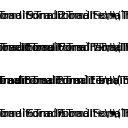

-Graphics-

```mathematica
SubsetEncoder[j_] := (
createList[l_]:= Subsets[l,{2}];
Return[
Graphics[
Polygon[createList[data[[j]]]],
 ImageSize->{64,64}]
]
)
SubsetEncoder[1]

PermutationEncoder[j_] := (
createList[l_]:= Permutations[l,{2}];
Return[
Graphics[
Polygon[createList[data[[j]]]],
 ImageSize->{64,64}]
]
)
PermutationEncoder[1]

(* Encoder changed *)
ScaledPermutationEncoder[j_] := (
createList[l_]:= Permutations[l,{2}];
max={};
min={};
For[i=1,i≤Dimensions[data][[2]],i++,AppendTo[max,Max[dataᵀ[[i]]]];
AppendTo[min,Min[dataᵀ[[i]]]];];
A=(data[[j]]-max)/(max-min);
Return[
Graphics[
Polygon[createList[A]],
 ImageSize->{64,64}]
]
)
ScaledPermutationEncoder[1]


Hippie[j_]:=(
l ={};
For[i=1, i≤ 3, i++,
d = IntegerDigits[IntegerPart[data[[j,i]]*10]];
If[Length[d] == 1,AppendTo[l,0]; AppendTo[l,d[[1]]], AppendTo[l,d[[1]]]; AppendTo[l,d[[2]]]];
];
p = {};
colors = {Green, Blue, Red, Gray, Black, Yellow, Purple, Orange};
For[i = 1, i ≤ Length[l], i++,
r = Length[l] -i + 1;
n = l[[i]]+3;
AppendTo[p,
{
colors[[i]],
Polygon[Table[{r*Cos[2π k/n],r*Sin[2π k/n]},{k,0,n-1}]]
}
]
];
Return[
Graphics[p, ImageSize->{64,64}]
]
)
Hippie[1]


Hippie2[j_]:= (
l ={};
c = {};
For[i=1, i≤ 3, i++,
d = IntegerDigits[IntegerPart[data[[j,i]]*10]];
If[Length[d] == 1, t= 0;g = d[[1]], t= d[[1]]; g = d[[2]]];
AppendTo[l,t];
AppendTo[c,g];
];
p = {};
For[i = 1, i ≤ Length[l], i++,
r = Length[l] -i + 1;
n = l[[i]]+3;
color = data[[j,i]]/9;
AppendTo[p,
{
RGBColor[color, color, color],
Polygon[Table[{r*Cos[2π k/n],r*Sin[2π k/n]},{k,0,n-1}]]
}
]
];
Return[
Graphics[p, ImageSize->{64,64}]
]
)
Hippie2[1]

RadarEncoder[j_]:=(
max={};
min={};
For[i=1,i≤Dimensions[data][[2]],i++,AppendTo[max,Max[dataᵀ[[i]]]];
AppendTo[min,Min[dataᵀ[[i]]]];];
α=2*π/(Dimensions[data][[2]]);
l={};
A=Abs[(data[[j]]-max)/(max-min)];
For[i=1,i≤Dimensions[data][[2]],i++,AppendTo[l,{A[[i]]*Cos[α*i],A[[i]]*Sin[α*i]}]];
Return[Graphics[{Polygon[l],Line[l]},PlotRange->{{-1,1},{-1,1}},ImageSize->{64,64}]])
RadarEncoder[1]

ColorEncoder[j_]:=(
max={};
min = {};
featuresSize = Dimensions[data][[2]];
For[i = 1, i≤ featuresSize, i++,
AppendTo[max, Max[dataᵀ[[i]]]];
AppendTo[min, Min[dataᵀ[[i]]]];
];
α = 2*π/featuresSize;
l = {};
A = Abs[(data[[j]] - max)/(max-min)];
For[i = 1, i≤ featuresSize, i++,
AppendTo[l, {A[[i]]*Cos[α*i],A[[i]]*Sin[α*i]}]
]
;
arcs = {};
(* We have to choose featuresSize colors *) 
featuresColors = {{1,0,0},{0,1,0},{0,0,1},{1,0,1}, {1,1,0}, {0,1,1}, {1,0.5,0.5}, {0.5,1,0.5}, {0.5,0.5,1}, {0.3,0.6,0.9}, {0.6,0.6,0.9},
{0.9,0.3,0.6}, {0, 0.8, 0.4}, {0.8, 0.9, 0.7}};
For[i = 1, i≤ featuresSize, i++,
AppendTo[arcs, {RGBColor[A[[i]]*featuresColors[[i]]],Disk[{0,0},2,{α*(i-1),α*i}]}]
];
Return[
Graphics[{arcs, Polygon[l]}, PlotRange->{{-1,1},{-1,1}}, ImageSize->{64,64}]
]
)
ColorEncoder[1]

EncodeData[j_,i_]:=(
l = RealDigits[data[[j,i]]];
If[data[[j,i]] > 0, PrependTo[l,"+"],PrependTo[l,"-"]];
If[l[[3]] < 0, l[[3]] = StringForm["-``",-l[[3]]],  l[[3]]=StringForm["+``",l[[3]]]];
l =Prepend[Append[l[[2,{1,2}]], l[[3]]], l[[1]]];
Return[
Text[StringForm["````````", l[[1]], l[[2]], l[[3]], l[[4]]]]
]
);

TextEncoder[j_]:= (
n = Dimensions[data][[2]];  (* Number of features *)
m = Ceiling[Sqrt[n]];  (* Grid Size *)
gl = {};
For[ i = 1, i≤ m, i ++,AppendTo[gl, {}]];
For[i = 1, i≤ n, i++,
AppendTo[gl[[Mod[i,m]+1]],
Graphics[EncodeData[j,i]]
]
];
For[i = n+1, i≤ m*m, i++,
AppendTo[gl[[Mod[i,m]+1]],
Graphics[Point[{0,0}]]
]
];
Return[
GraphicsGrid[gl,Frame->None, ImageSize->{128,128}]
]
)
TextEncoder[1]

ColorEncoder[j_]:=(
l = {};
colors = Subsets[data[[j]], {3}];
n = Length[colors];
For[i = 1, i ≤ n, i++,
AppendTo[l, {RGBColor[colors[[i]]],Disk[{0,0},n-i]}]
];
Return[
Graphics[l, ImageSize->{128,128}]
]
)
ColorEncoder[1]
```

```mathematica
For[j = 1, j ≤  Dimensions[data][[1]] , j++, 
Export[ToString[StringForm["/home/allan/Git/data_encoding/conv_leaf/images/image_``_``.jpg",labels[[j]],j]],
TextEncoder[j]
]
]
```